# Numerical Diagonalisation of an arbitrary Hamiltonian

## Initialisation

#### Old initialisation (continuous)

```mathematica
ClearAll["Global`*"]
```

```mathematica
AutoCollapse[] := (
  If[$FrontEnd =!= $Failed, 
   SelectionMove[EvaluationNotebook[], All, GeneratedCell];
   FrontEndTokenExecute["SelectionCloseUnselectedCells"]])
```

```mathematica
colorBar[title_:"arg[ψ]"] :=
	BarLegend[
		{"Rainbow", {-π, π}}, 
		LegendLabel -> title,
		"Ticks" -> {-3.14, -3.14/2, 0, 3.14/2, 3.14}, 
		"TickLabels" -> {"-π", "-π/2", "0", "π/2", "π"}
	]

colorBarNorm[title_] :=
	BarLegend[
		"Rainbow", 
		LegendLabel -> title
	]

plotWavefunction[psi_, {r_, range__}, showbar_:True, title_:Abs[ψ]^2, legendpsi_:ψ, plotrange_:All, ticks_:Automatic] :=
	ReplaceAll[
		Plot[
			Abs[psi]^2, {r, range}, 
			AxesLabel -> {r, title},
			PlotRange -> plotrange,
			ColorFunction -> (ColorData["Rainbow"][Rescale[Arg[psi /. r -> #], {-π, π}]] &),
			ColorFunctionScaling -> False,
			Ticks -> ticks,
			Filling -> Axis,
			PlotLegends -> If[showbar, colorBarNorm["arg[" <> ToString[legendpsi] <> "] / 2π"], None]
		],
		Line[pts_, _] :> {Black, Line[pts]}
	]
```

```mathematica
simulateWavefunction[psi_, potential_, {r_, domain__}, {_, times__}] :=
	NDSolveValue[
		{ⅈ Derivative[0,1][ψ][r, τ] ==  -Derivative[2,0][ψ][r, τ] / 2 + ψ[r, τ] potential, ψ[r, 0] == psi },
		ψ, 
		{r, domain}, 
		{τ, times},
		Method -> {"FiniteElement"}
	] 
	

Off[NDSolveValue::bcart]
Off[NDSolveValue::femcscd]
```

```mathematica
hamiltonian[psi_, potential_, r_] := 
	-1/2 D[psi, {r,2}] + potential psi
```

```mathematica
expectedEnergy[psi_, potential_,  r_] :=
	Integrate[
		(Conjugate[psi] /. Conjugate[r] -> r)
		(hamiltonian[psi, potential, r]),
		{r, -∞, ∞}
	]
```

```mathematica
quickNormalise[psi_, r_:x] := 
	psi / Sqrt[NIntegrate[
					Abs[psi]^2, {r, -∞, ∞}, 
					Method -> {Automatic, "SymbolicProcessing" -> 0}]]
```

### new initialisation (discrete)

## Testing

Give me a discretised potential

```mathematica
potentialCont[x_] = 1/2 x^2;

x0 = -5;
x1 = -x0;
Δx = 0.05;

grid = Range[x0, x1, Δx];
gridsize = Length[grid];
potentialDisc = Map[potentialCont, grid];
```

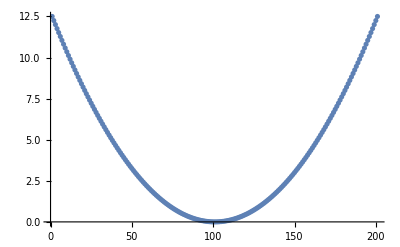

```mathematica
ListPlot[potentialDisc]
```

```mathematica
(* potential center is at (x1 - x0)/Δx/2 *)
```

```mathematica
laplacianMatrix = SparseArray[{{i_,i_}:>-2,{i_,j_}:>1/;Abs[i-j]==1},{gridsize, gridsize}];
laplacianMatrix = SparseArray[
{
{i_,i_}:>-5/2,
{i_,j_}:>4/3/;Abs[i-j]==1,
{i_,j_} :> -1/12  /; Abs[i-j] == 2
},{gridsize, gridsize}];
kineticMatrix = -1/2 laplacianMatrix / Δx ;
potentialMatrix = SparseArray[{i_, i_} :> potentialDisc[[i]], {gridsize, gridsize}];
hamiltonianMatrix = kineticMatrix + potentialMatrix;


(* laplacianMatrix // MatrixForm *)
```

$Aborted[]

```mathematica
numModes = 10;
precision = 30;
{eigenvalues, eigenfunctions} = N[Eigensystem[hamiltonianMatrix, -numModes], precision];
{eigenvalues, eigenfunctions} = {eigenvalues[[#]], eigenfunctions[[#]]}& @ Ordering[eigenvalues];
```

```mathematica
eigenvalues * 0.5/eigenvalues[[1]]
```

{0.5,1.49999,2.49997,3.49993,4.49985,5.49972,6.49953,7.49928,8.49895,9.49854}

```mathematica
potentialCenter = IntegerPart[(x1 - x0)/Δx / 2];


Manipulate[
	ListLinePlot[
		 MapThread[{#1, #2}&,{grid, eigenfunctions[[n]]}],
		PlotRange->All
	],
	{n, 1,  numModes, 1}
]
```

```mathematica
(* x[i-1] -> x0 + (x1-x0) i / Δx *)
(* i -> (x[i-1] - x0) Δx / (x1-x0) *)

plotDiscreteψ[psi_, grid_] :=
	ListLinePlot[
		MapThread[{#1, #2}&, {grid, Abs[psi]^2}],
		ColorFunctionScaling-> False,
		ColorFunction -> (ColorData["Rainbow"][Rescale[Arg[psi[[
			IntegerPart[ (# - x0) Δx / (x1 - x0)]
			]]], {-π, π}]] &),
		PlotRange->All,
		Filling->Axis
	]
```

```mathematica
eigenfunctions[[1]][[1]]
```

-1.19374×10^-18

```mathematica
plotDiscreteψ[eigenfunctions[[1]], grid]
```

-Graphics-

```mathematica
(* x[i-1] -> x0 + (x1-x0) i / Δx *)
(* i -> (x[i-1] - x0) Δx / (x1-x0) *)
```